```mathematica
F[x_]:=(x^(n-1))/(x^2+1)^((n+2)/2)/;n∈ℤ
```

```mathematica
F[a]
```

F[a]

```mathematica
Integrate[F[x],x]
```

∫F[x]ⅆx

```mathematica
Integrate[F[x],{x,0, +∞},Assumptions-> n>0]
```

Integrate[F[x],{x,0,∞},Assumptions→n>0]

```mathematica
Sum[(x^n (1+x^2)^(-n/2))/n,{n,1,∞}]
```

-Log[(-x+√(1+x^2))/(√(1+x^2))]

```mathematica
f1[ξ_,n_]:=Sum[(x^n (1+x^2)^(-n/2))/n,{x,0,ξ}]
```

```mathematica
Manipulate[Plot[f1[x,n],{x,1,10}],{n,1,200}]
```

```mathematica
f0[x_]:=(x-√(1+x^2))/(√(1+x^2))+1;f2[x_]:=x/√(1+x^2);soft[x_]:=x/(1+Abs[x])
```

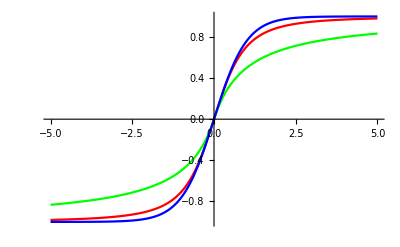

```mathematica
Plot[{f2[x],soft[x],Tanh[x]},{x,-5,5},PlotStyle->{Red, Green, Blue}]
```

```mathematica
fd[x_]=f2'[x]
```

-x^2/((1+x^2)^(3/2))+1/(√(1+x^2))

```mathematica
Integrate[f2[x],x]
```

√(1+x^2)

```mathematica
f4[x_]:=-Log[-(x-√(1+x^2))/(√(1+x^2))]
```

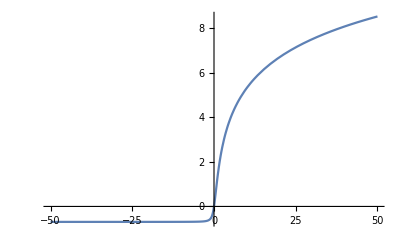

```mathematica
Plot[f4[x],{x,-50,50}]
```

```mathematica
soft'[x]//FullSimplify
```

(1+Abs[x]-x Abs'[x])/(1+Abs[x])^2

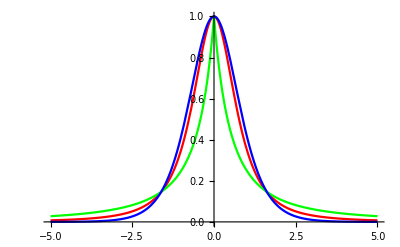

```mathematica
Plot[{f2'[x],1/(1+Abs[x])^2,Tanh'[x]},{x,-5,5},PlotStyle->{Red, Green, Blue}]
```

```mathematica
Integrate[soft[x],x, Assumptions->x<0]
```

-x-Log[1-x]

```mathematica
Integrate[soft[x],x, Assumptions->x>=0]
```

x-Log[1+x]

```mathematica
Integrate[Tanh[x],x]
```

Log[Cosh[x]]

```mathematica
Integrate[f2[x],x]
```

√(1+x^2)

```mathematica
Is[x_]:=If[x>=0,x-Log[1+x],-x-Log[1-x]];
Itans[x_]:=√(1+x^2)-1;
Itanh[x_]:=Log[Cosh[x]];
```

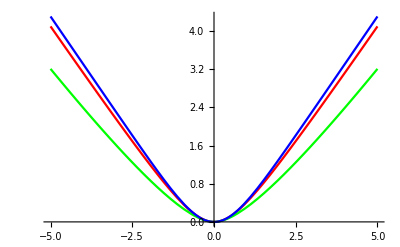

```mathematica
Plot[{Itans[x],Is[x],Itanh[x]},{x,-5,5},PlotStyle->{Red, Green, Blue}]
```

```mathematica
fd2[x_]:=(1-f2[x]^2)f2[x]/x
```

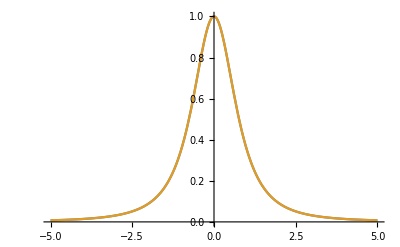

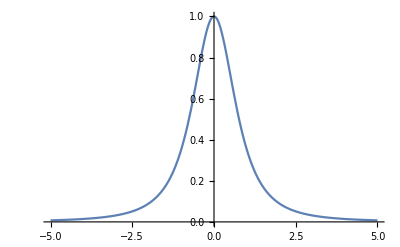

```mathematica
Plot[{fd2[x],f2'[x]},{x,-5,5}]
```

```mathematica
Bp1[x_]:=x Tanh'[x]; Bp2[x_]:=x fd2[x];Bp3[x_]:=x/(1+Abs[x])^2;
```

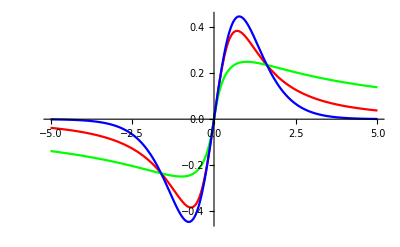

```mathematica
Plot[{Bp2[x],Bp3[x],Bp1[x]},{x,-5,5},PlotStyle->{Red, Green, Blue}]
```